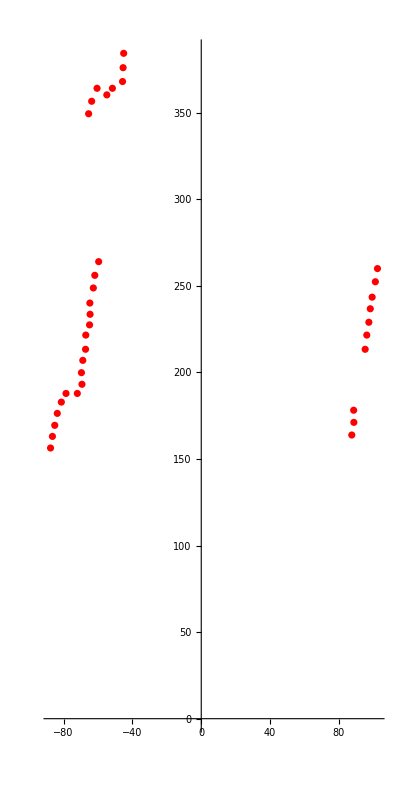

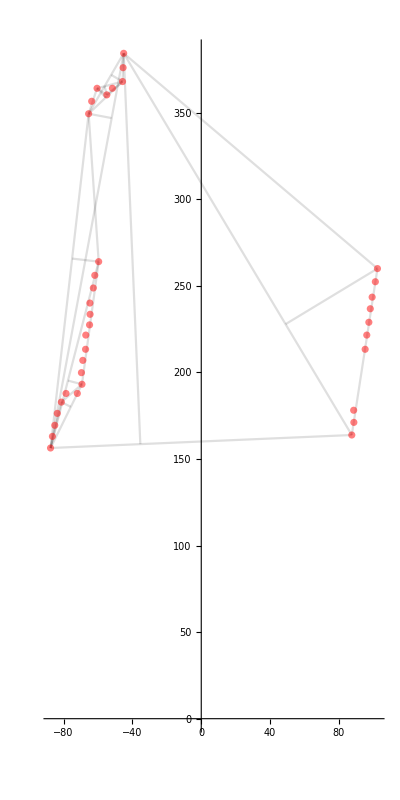

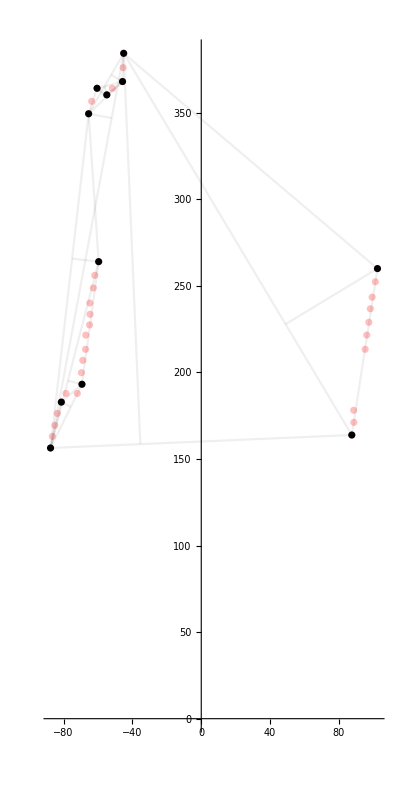

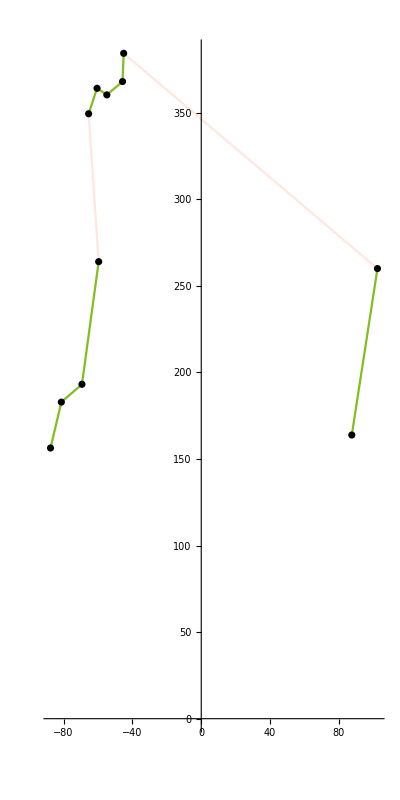

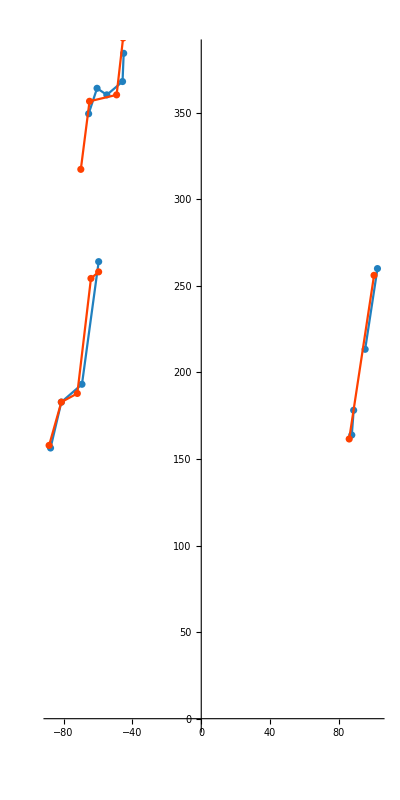

```mathematica
f1p01x=-87.553008;
f1p02x=-86.4554445;
f1p03x=-85.1054589;
f1p04x=-83.63416365;
f1p05x=-81.2778156;
f1p06x=-78.5697921;
f1p07x=-71.9949141;
f1p08x=-69.29441775;
f1p09x=-69.6002301;
f1p10x=-68.8139055;
f1p11x=-67.208697;
f1p12x=-67.07828475;
f1p13x=-64.8843831;
f1p14x=-64.5811965;
f1p15x=-64.69848;
f1p16x=-62.6903064;
f1p17x=-61.841664;
f1p18x=-59.59244655;
f1p19x=-65.42511255;
f1p20x=-63.6534315;
f1p21x=-60.53229;
f1p22x=-54.8561187;
f1p23x=-51.611742;
f1p24x=-45.72463545;
f1p25x=-45.40289355;
f1p26x=-45.0603207;
f1p27x=-44.7165225;
f1p27x=102.36486375;
f1p28x=101.13811335;
f1p29x=99.2747061;
f1p30x=98.19937395;
f1p31x=97.36753635;
f1p32x=96.158466;
f1p33x=95.21232075;
f1p34x=88.5409902;
f1p35x=88.6551228;
f1p36x=87.4532295;
f1p01y=156.3;
f1p02y=163.0;
f1p03y=169.4;
f1p04y=176.3;
f1p05y=182.8;
f1p06y=187.8;
f1p07y=187.8;
f1p08y=193.1;
f1p09y=199.8;
f1p10y=206.9;
f1p11y=213.3;
f1p12y=221.5;
f1p13y=227.4;
f1p14y=233.5;
f1p15y=240.0;
f1p16y=248.7;
f1p17y=256.0;
f1p18y=263.9;
f1p19y=349.3;
f1p20y=356.5;
f1p21y=364.0;
f1p22y=360.2;
f1p23y=364.0;
f1p24y=367.9;
f1p25y=375.9;
f1p26y=384.2;
f1p27y=393.0;
f1p27y=259.9;
f1p28y=252.3;
f1p29y=243.4;
f1p30y=236.7;
f1p31y=228.9;
f1p32y=221.5;
f1p33y=213.3;
f1p34y=178.1;
f1p35y=171.1;
f1p36y=163.8;

f2p01x=-88.393248;
f2p02x=-86.8797657;
f2p03x=-86.1032439;
f2p04x=-83.9427768;
f2p05x=-81.2778156;
f2p06x=-75.3737292;
f2p07x=-71.9949141;
f2p08x=-71.756496;
f2p09x=-71.10898605;
f2p10x=-69.6786525;
f2p11x=-68.500566;
f2p12x=-68.0153274;
f2p13x=-67.033647;
f2p14x=-65.95884;
f2p15x=-65.26196595;
f2p16x=-64.0767024;
f2p17x=-59.615028;
f2p18x=-69.9625836;
f2p19x=-69.6635982;
f2p20x=-69.823944;
f2p21x=-68.836662;
f2p22x=-67.7961648;
f2p23x=-64.901538;
f2p24x=-61.1572185;
f2p25x=-55.4866488;
f2p26x=-49.1813478;
f2p27x=-47.7504891;
f2p27x=-45.404469;
f2p28x=100.380672;
f2p29x=98.82430245;
f2p30x=97.73514135;
f2p31x=96.3009567;
f2p32x=95.76477855;
f2p33x=94.1772501;
f2p34x=93.6829089;
f2p35x=91.8161757;
f2p36x=91.4503212;
f2p37x=89.8944768;
f2p38x=88.9576092;
f2p39x=88.1198199;
f2p40x=87.0646185;
f2p41x=85.942548;
f2p01y=157.8;
f2p02y=163.8;
f2p03y=170.2;
f2p04y=176.3;
f2p05y=182.8;
f2p06y=184.8;
f2p07y=187.8;
f2p08y=195.2;
f2p09y=202.1;
f2p10y=209.5;
f2p11y=217.4;
f2p12y=225.9;
f2p13y=233.5;
f2p14y=240.0;
f2p15y=246.9;
f2p16y=254.2;
f2p17y=258.0;
f2p18y=317.2;
f2p19y=326.2;
f2p20y=332.4;
f2p21y=339.0;
f2p22y=345.8;
f2p23y=356.5;
f2p24y=356.5;
f2p25y=360.2;
f2p26y=360.2;
f2p27y=384.2;
f2p27y=393.0;
f2p28y=256.0;
f2p29y=248.7;
f2p30y=241.7;
f2p31y=235.1;
f2p32y=228.9;
f2p33y=218.7;
f2p34y=210.7;
f2p35y=203.3;
f2p36y=196.4;
f2p37y=188.8;
f2p38y=182.8;
f2p39y=175.4;
f2p40y=168.6;
f2p41y=161.5;


ab01 = {f1p01x - f1p36x, f1p01y - f1p36y};
ac01 = {f1p26x - f1p36x, f1p26y - f1p36y};
ab01n = Normalize[ab01];
d01 = Dot[ab01n, ac01] * ab01n  + {f1p36x, f1p36y};


ab02 = {f1p26x - f1p01x, f1p26y - f1p01y};
ac02 = {f1p19x - f1p01x, f1p19y - f1p01y};
ab02n = Normalize[ab02];
d02 = Dot[ab02n, ac02] * ab02n + {f1p01x, f1p01y};


ab03 = {f1p26x - f1p36x, f1p26y - f1p36y};
ac03 = {f1p27x - f1p36x, f1p27y - f1p36y};
ab03n = Normalize[ab03];
d03 = Dot[ab03n, ac03] * ab03n + {f1p36x, f1p36y};


ab04 = {f1p19x - f1p01x, f1p19y - f1p01y};
ac04 = {f1p18x - f1p01x, f1p18y - f1p01y};
ab04n = Normalize[ab04];
d04 = Dot[ab04n, ac04] * ab04n + {f1p01x, f1p01y};


ab05 = {f1p26x - f1p19x, f1p26y - f1p19y};
ac05 = {f1p24x - f1p19x, f1p24y - f1p19y};
ab05n = Normalize[ab05];
d05 = Dot[ab05n, ac05] * ab05n + {f1p19x, f1p19y};


ab06 = {f1p18x - f1p01x, f1p18y - f1p01y};
ac06 = {f1p08x - f1p01x, f1p08y - f1p01y};
ab06n = Normalize[ab06];
d06 = Dot[ab06n, ac06] * ab06n + {f1p01x, f1p01y};


ab07 = {f1p24x - f1p19x, f1p24y - f1p19y};
ac07 = {f1p21x - f1p19x, f1p21y - f1p19y};
ab07n = Normalize[ab07];
d07 = Dot[ab07n, ac07] * ab07n + {f1p19x, f1p19y};


ab08 = {f1p08x - f1p01x, f1p08y - f1p01y};
ac08 = {f1p05x - f1p01x, f1p05y - f1p01y};
ab08n = Normalize[ab08];
d08 = Dot[ab08n, ac08] * ab08n + {f1p01x, f1p01y};


ab09 = {f1p24x - f1p21x, f1p24y - f1p21y};
ac09 = {f1p22x - f1p21x, f1p22y - f1p21y};
ab09n = Normalize[ab09];
d09 = Dot[ab09n, ac09] * ab09n + {f1p21x, f1p21y};



ListPlot[{{f1p01x,f1p01y},{f1p02x,f1p02y},{f1p03x,f1p03y},{f1p04x,f1p04y},{f1p05x,f1p05y},{f1p06x,f1p06y},{f1p07x,f1p07y},{f1p08x,f1p08y},{f1p09x,f1p09y},{f1p10x,f1p10y},{f1p11x,f1p11y},{f1p12x,f1p12y},{f1p13x,f1p13y},{f1p14x,f1p14y},{f1p15x,f1p15y},{f1p16x,f1p16y},{f1p17x,f1p17y},{f1p18x,f1p18y},{f1p19x,f1p19y},{f1p20x,f1p20y},{f1p21x,f1p21y},{f1p22x,f1p22y},{f1p23x,f1p23y},{f1p24x,f1p24y},{f1p25x,f1p25y},{f1p26x,f1p26y},{f1p27x,f1p27y},{f1p28x,f1p28y},{f1p29x,f1p29y},{f1p30x,f1p30y},{f1p31x,f1p31y},{f1p32x,f1p32y},{f1p33x,f1p33y},{f1p34x,f1p34y},{f1p35x,f1p35y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,0,0]]



Show[
ListPlot[{{f1p01x,f1p01y},{f1p02x,f1p02y},{f1p03x,f1p03y},{f1p04x,f1p04y},{f1p05x,f1p05y},{f1p06x,f1p06y},{f1p07x,f1p07y},{f1p08x,f1p08y},{f1p09x,f1p09y},{f1p10x,f1p10y},{f1p11x,f1p11y},{f1p12x,f1p12y},{f1p13x,f1p13y},{f1p14x,f1p14y},{f1p15x,f1p15y},{f1p16x,f1p16y},{f1p17x,f1p17y},{f1p18x,f1p18y},{f1p19x,f1p19y},{f1p20x,f1p20y},{f1p21x,f1p21y},{f1p22x,f1p22y},{f1p23x,f1p23y},{f1p24x,f1p24y},{f1p25x,f1p25y},{f1p26x,f1p26y},{f1p27x,f1p27y},{f1p28x,f1p28y},{f1p29x,f1p29y},{f1p30x,f1p30y},{f1p31x,f1p31y},{f1p32x,f1p32y},{f1p33x,f1p33y},{f1p34x,f1p34y},{f1p35x,f1p35y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,1,1]],


ListLinePlot[{{f1p01x,f1p01y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p26x,f1p26y},d01},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],


ListLinePlot[{{f1p01x,f1p01y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p26x,f1p26y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p19x,f1p19y},d02},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p27x,f1p27y},d03},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],


ListLinePlot[{{f1p01x,f1p01y},{f1p19x,f1p19y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p19x,f1p19y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p26x,f1p26y},{f1p27x,f1p27y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p27x,f1p27y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p18x,f1p18y},d04},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p24x,f1p24y},d05},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],


ListLinePlot[{{f1p01x,f1p01y},{f1p18x,f1p18y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p18x,f1p18y},{f1p19x,f1p19y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p19x,f1p19y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p24x,f1p24y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p08x,f1p08y},d06},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p21x,f1p21y},d07},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],


ListLinePlot[{{f1p01x,f1p01y},{f1p08x,f1p08y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p08x,f1p08y},{f1p18x,f1p18y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p19x,f1p19y},{f1p21x,f1p21y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p21x,f1p21y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p05x,f1p05y},d08},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p22x,f1p22y},d09},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],


ListLinePlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p05x,f1p05y},{f1p08x,f1p08y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p21x,f1p21y},{f1p22x,f1p22y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],
ListLinePlot[{{f1p22x,f1p22y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.125]],



ListPlot[{{f1p01x,f1p01y},{f1p02x,f1p02y},{f1p03x,f1p03y},{f1p04x,f1p04y},{f1p05x,f1p05y},{f1p06x,f1p06y},{f1p07x,f1p07y},{f1p08x,f1p08y},{f1p09x,f1p09y},{f1p10x,f1p10y},{f1p11x,f1p11y},{f1p12x,f1p12y},{f1p13x,f1p13y},{f1p14x,f1p14y},{f1p15x,f1p15y},{f1p16x,f1p16y},{f1p17x,f1p17y},{f1p18x,f1p18y},{f1p19x,f1p19y},{f1p20x,f1p20y},{f1p21x,f1p21y},{f1p22x,f1p22y},{f1p23x,f1p23y},{f1p24x,f1p24y},{f1p25x,f1p25y},{f1p26x,f1p26y},{f1p27x,f1p27y},{f1p28x,f1p28y},{f1p29x,f1p29y},{f1p30x,f1p30y},{f1p31x,f1p31y},{f1p32x,f1p32y},{f1p33x,f1p33y},{f1p34x,f1p34y},{f1p35x,f1p35y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,0,0,0.5]]
]

Show[
ListPlot[{{f1p01x,f1p01y},{f1p02x,f1p02y},{f1p03x,f1p03y},{f1p04x,f1p04y},{f1p05x,f1p05y},{f1p06x,f1p06y},{f1p07x,f1p07y},{f1p08x,f1p08y},{f1p09x,f1p09y},{f1p10x,f1p10y},{f1p11x,f1p11y},{f1p12x,f1p12y},{f1p13x,f1p13y},{f1p14x,f1p14y},{f1p15x,f1p15y},{f1p16x,f1p16y},{f1p17x,f1p17y},{f1p18x,f1p18y},{f1p19x,f1p19y},{f1p20x,f1p20y},{f1p21x,f1p21y},{f1p22x,f1p22y},{f1p23x,f1p23y},{f1p24x,f1p24y},{f1p25x,f1p25y},{f1p26x,f1p26y},{f1p27x,f1p27y},{f1p28x,f1p28y},{f1p29x,f1p29y},{f1p30x,f1p30y},{f1p31x,f1p31y},{f1p32x,f1p32y},{f1p33x,f1p33y},{f1p34x,f1p34y},{f1p35x,f1p35y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,0,0,0.25]],


ListLinePlot[{{f1p01x,f1p01y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p26x,f1p26y},d01},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],


ListLinePlot[{{f1p01x,f1p01y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p26x,f1p26y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p19x,f1p19y},d02},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p27x,f1p27y},d03},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],


ListLinePlot[{{f1p01x,f1p01y},{f1p19x,f1p19y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p19x,f1p19y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p26x,f1p26y},{f1p27x,f1p27y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p27x,f1p27y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p18x,f1p18y},d04},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p24x,f1p24y},d05},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],


ListLinePlot[{{f1p01x,f1p01y},{f1p18x,f1p18y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p18x,f1p18y},{f1p19x,f1p19y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p19x,f1p19y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p24x,f1p24y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p08x,f1p08y},d06},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p21x,f1p21y},d07},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],


ListLinePlot[{{f1p01x,f1p01y},{f1p08x,f1p08y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p08x,f1p08y},{f1p18x,f1p18y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p19x,f1p19y},{f1p21x,f1p21y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p21x,f1p21y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p05x,f1p05y},d08},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p22x,f1p22y},d09},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],


ListLinePlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p05x,f1p05y},{f1p08x,f1p08y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p21x,f1p21y},{f1p22x,f1p22y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],
ListLinePlot[{{f1p22x,f1p22y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0, 0.0625]],



ListPlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}, {f1p08x,f1p08y},{f1p18x,f1p18y}, {f1p19x,f1p19y},{f1p21x,f1p21y}, {f1p22x,f1p22y},{f1p24x,f1p24y}, {f1p26x,f1p26y},{f1p27x,f1p27y}, {f1p36x,f1p36y}}, AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0]]
]



Show[
ListPlot[{{f1p01x,f1p01y},{f1p02x,f1p02y},{f1p03x,f1p03y},{f1p04x,f1p04y},{f1p05x,f1p05y},{f1p06x,f1p06y},{f1p07x,f1p07y},{f1p08x,f1p08y},{f1p09x,f1p09y},{f1p10x,f1p10y},{f1p11x,f1p11y},{f1p12x,f1p12y},{f1p13x,f1p13y},{f1p14x,f1p14y},{f1p15x,f1p15y},{f1p16x,f1p16y},{f1p17x,f1p17y},{f1p18x,f1p18y},{f1p19x,f1p19y},{f1p20x,f1p20y},{f1p21x,f1p21y},{f1p22x,f1p22y},{f1p23x,f1p23y},{f1p24x,f1p24y},{f1p25x,f1p25y},{f1p26x,f1p26y},{f1p27x,f1p27y},{f1p28x,f1p28y},{f1p29x,f1p29y},{f1p30x,f1p30y},{f1p31x,f1p31y},{f1p32x,f1p32y},{f1p33x,f1p33y},{f1p34x,f1p34y},{f1p35x,f1p35y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,1,1]],


ListLinePlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],
ListLinePlot[{{f1p05x,f1p05y},{f1p08x,f1p08y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],
ListLinePlot[{{f1p08x,f1p08y},{f1p18x,f1p18y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],

ListLinePlot[{{f1p18x,f1p18y},{f1p19x,f1p19y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,0.25,0,0.125]],

ListLinePlot[{{f1p19x,f1p19y},{f1p21x,f1p21y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],
ListLinePlot[{{f1p21x,f1p21y},{f1p22x,f1p22y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],
ListLinePlot[{{f1p22x,f1p22y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],
ListLinePlot[{{f1p24x,f1p24y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],

ListLinePlot[{{f1p26x,f1p26y},{f1p27x,f1p27y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,0.25,0,0.125]],

ListLinePlot[{{f1p27x,f1p27y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.5,0.75,0.125]],


ListPlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}, {f1p08x,f1p08y},{f1p18x,f1p18y}, {f1p19x,f1p19y},{f1p21x,f1p21y}, {f1p22x,f1p22y},{f1p24x,f1p24y}, {f1p26x,f1p26y},{f1p27x,f1p27y}, {f1p36x,f1p36y}}, AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0,0,0]]
]










Show[
ListPlot[{{f1p01x,f1p01y},{f1p02x,f1p02y},{f1p03x,f1p03y},{f1p04x,f1p04y},{f1p05x,f1p05y},{f1p06x,f1p06y},{f1p07x,f1p07y},{f1p08x,f1p08y},{f1p09x,f1p09y},{f1p10x,f1p10y},{f1p11x,f1p11y},{f1p12x,f1p12y},{f1p13x,f1p13y},{f1p14x,f1p14y},{f1p15x,f1p15y},{f1p16x,f1p16y},{f1p17x,f1p17y},{f1p18x,f1p18y},{f1p19x,f1p19y},{f1p20x,f1p20y},{f1p21x,f1p21y},{f1p22x,f1p22y},{f1p23x,f1p23y},{f1p24x,f1p24y},{f1p25x,f1p25y},{f1p26x,f1p26y},{f1p27x,f1p27y},{f1p28x,f1p28y},{f1p29x,f1p29y},{f1p30x,f1p30y},{f1p31x,f1p31y},{f1p32x,f1p32y},{f1p33x,f1p33y},{f1p34x,f1p34y},{f1p35x,f1p35y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,1,1]],
ListPlot[{{f2p01x,f2p01y},{f2p02x,f2p02y},{f2p03x,f2p03y},{f2p04x,f2p04y},{f2p05x,f2p05y},{f2p06x,f2p06y},{f2p07x,f2p07y},{f2p08x,f2p08y},{f2p09x,f2p09y},{f2p10x,f2p10y},{f2p11x,f2p11y},{f2p12x,f2p12y},{f2p13x,f2p13y},{f2p14x,f2p14y},{f2p15x,f2p15y},{f2p16x,f2p16y},{f2p17x,f2p17y},{f2p18x,f2p18y},{f2p19x,f2p19y},{f2p20x,f2p20y},{f2p21x,f2p21y},{f2p22x,f2p22y},{f2p23x,f2p23y},{f2p24x,f2p24y},{f2p25x,f2p25y},{f2p26x,f2p26y},{f2p27x,f2p27y},{f2p28x,f2p28y},{f2p29x,f2p29y},{f2p30x,f2p30y},{f2p31x,f2p31y},{f2p32x,f2p32y},{f2p33x,f2p33y},{f2p34x,f2p34y},{f2p35x,f2p35y},{f2p36x,f2p36y},{f2p37x,f2p37y},{f2p38x,f2p38y},{f2p39x,f2p39y},{f2p40x,f2p40y},{f2p41x,f2p41y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,1,1]],

ListLinePlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p05x,f1p05y},{f1p08x,f1p08y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p08x,f1p08y},{f1p18x,f1p18y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p19x,f1p19y},{f1p21x,f1p21y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p21x,f1p21y},{f1p22x,f1p22y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p22x,f1p22y},{f1p24x,f1p24y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p24x,f1p24y},{f1p26x,f1p26y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p27x,f1p27y},{f1p33x,f1p33y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],
ListLinePlot[{{f1p34x,f1p34y},{f1p36x,f1p36y}},AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],

ListPlot[{{f1p01x,f1p01y},{f1p05x,f1p05y}, {f1p08x,f1p08y},{f1p18x,f1p18y}, {f1p19x,f1p19y},{f1p21x,f1p21y}, {f1p22x,f1p22y},{f1p24x,f1p24y}, {f1p26x,f1p26y},{f1p27x,f1p27y}, {f1p33x,f1p33y}, {f1p34x,f1p34y}, {f1p36x,f1p36y}}, AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[0.125,0.5,0.75]],


ListLinePlot[{{f2p01x,f2p01y},{f2p05x,f2p05y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p05x,f2p05y},{f2p07x,f2p07y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p07x,f2p07y},{f2p16x,f2p16y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p16x,f2p16y},{f2p17x,f2p17y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p18x,f2p18y},{f2p23x,f2p23y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p23x,f2p23y},{f2p26x,f2p26y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p26x,f2p26y},{f2p27x,f2p27y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],
ListLinePlot[{{f2p28x,f2p28y},{f2p41x,f2p41y}},AxesOrigin->{0,0},AspectRatio->2,PlotStyle->RGBColor[1,0.25,0]],


ListPlot[{{f2p01x,f2p01y},{f2p05x,f2p05y}, {f2p07x,f2p07y},{f2p16x,f2p16y},{f2p17x,f2p17y},{f2p18x,f2p18y},{f2p23x,f2p23y},{f2p26x,f2p26y},{f2p27x,f2p27y},{f2p28x,f2p28y},{f2p41x,f2p41y}}, AxesOrigin->{0,0}, AspectRatio->2, PlotStyle->RGBColor[1,0.25,0]]
]

Remove["Global`*"]
```